```mathematica
PrependTo[$Path,"/Users/annils14/Documents/KerrModes"];PrependTo[$Path,"~/Research/KerrQNM/KerrModes"];
Needs["KerrTTML`"]
SetSpinWeight[-2]
SelectMode[PolynomialMode]
```

All KerrMode routines (TTML) set for Spin-Weight s = -2

Mode set to find Polynomial solutions

```mathematica
SchTTMLTable[2]=2;
SchTTMLTable[2,0]={-2.00*I,0,0,0,0};
SchTTMLTable[2,1]={-2.00*I,0,0,0,0};
SchTTMLTable[3]=2;
SchTTMLTable[3,0]={-10.0*I,0,0,0,0};
SchTTMLTable[3,1]={-10.0*I,0,0,0,0};
```

```mathematica
SchwarzschildTTML[2,0]
```

Computing (l=2,n=0)

{-2. ⅈ,0,300,-14,0}

```mathematica
Save["/Users/annils14/Documents/KerrModes/KerrTTMLTable_00.dat",KerrTTML]
```

```mathematica
<<"/Users/annils14/Documents/KerrModes/KerrTTMLTable_00.dat";
```

```mathematica
<<"/Users/annils14/Documents/KerrModes/KerrTTMLTable_p01.dat";
```

```mathematica
<<"/Users/annils14/Documents/KerrModes/KerrTTMLTable_p02.dat";
```

```mathematica
<<"/Users/annils14/Documents/KerrModes/KerrTTMLTable_p03.dat";
```

```mathematica
<<"/Users/annils14/Documents/KerrModes/KerrTTMLTable_p04.dat";
```

```mathematica
<<"/Users/annils14/Documents/KerrModes/KerrTTMLTable_p05.dat";
```

```mathematica
<<"~/Research/KerrQNM/KerrModes/KerrTTMLTable_00.dat";
```

```mathematica
<<"~/Research/KerrQNM/KerrModes/KerrTTMLTable_p01.dat";
```

```mathematica
<<"~/Research/KerrQNM/KerrModes/KerrTTMLTable_p02.dat";
```

```mathematica
<<"~/Research/KerrQNM/KerrModes/KerrTTMLTable_p03.dat";
```

```mathematica
<<"~/Research/KerrQNM/KerrModes/KerrTTMLTable_p04.dat";
```

```mathematica
<<"~/Research/KerrQNM/KerrModes/KerrTTMLTable_p05.dat";
```

```mathematica
KerrTTML[2,0,{0,0}][[-1]]
```

{8101001/16384000,{-2.59221938844357377362308×10^-27-3.32932464333632508809299 ⅈ,0,300,-8,1.05427856406349503051469×10^-19,300,0,0.654387451804623391671247,24},{5.31169089006987495148787-1.86929049226304246652264×10^-27 ⅈ,12,{0.926314398664427651686731,-2.43605512448961034437431×10^-28-0.362297525389928649821131 ⅈ,-0.101203172569303999014166+1.44835657915437095439063×10^-28 ⅈ,4.52699248059806435096392×10^-29+0.020691886304687763601274 ⅈ,0.00341752527281805138651751-1.01091317404582626241193×10^-29 ⅈ,-1.74497194733624481485521×10^-30-0.000468058577520540482725929 ⅈ,-0.0000551013052586024172915862+2.48084298442211282297944×10^-31 ⅈ,2.98995697994554160239674×10^-32+5.66643235812711576651505×10^-6 ⅈ,5.18537495346009658744474×10^-7-3.13850162493409875158105×10^-33 ⅈ,-2.91415986051870476043666×10^-34-4.26754202753149016890482×10^-8 ⅈ,-3.19443226670194558835269×10^-9+2.42952301019190785071037×10^-35 ⅈ,1.83926163720485453009745×10^-36+2.19370530272997909914795×10^-10 ⅈ}}}

```mathematica
KerrTTML[2,0,{0,2}]=KerrTTML[2,0,{0,1}];
```

```mathematica
KerrModeMakeMultiplet[2,0,0]
```

```mathematica
?ShortenModeSequence
```

ShortenModeSequence[l,m,n,N] removes the first N elements of the Mode sequence (l,m,n)
if N>0, and removes the last N elements if N<0.

Options:
	 ShortenBy→Drop : Drop, Take
		 If 'Take' is chosen, the first N elemets are kept if N>0, and the last N elements
		 are kept if N<0.

```mathematica
1253-563
```

690

```mathematica
Length[KerrTTML[2,0,{0,0}]]
```

573

```mathematica
ShortenModeSequence[2,0,{0,2},-690]
```

Original Length of `1`[`2`,`3`,`4`] = `5`KerrTTML20{0,2}2436

Removing last -690 elements

```mathematica
KerrTTMLSequence[2,0,{0,1},-8,ModeGuess->{0.0004334-3.331*I,4},MaxΔω->10,SeqDirection->Backward]
```

$Aborted

```mathematica
ShortenModeSequence[2,0,{0,1},-100]
```

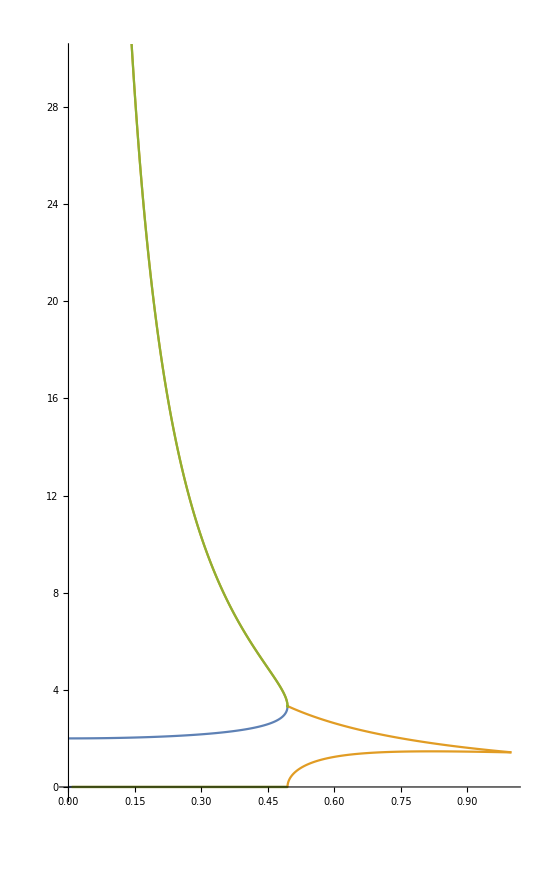

```mathematica
Show[ListLinePlot[{KerraOmegaList[2,0,{0,0},Re],KerraOmegaList[2,0,{0,1},Re],KerraOmegaList[2,0,{0,2},Re]},PlotRange->All],ListLinePlot[{KerraOmegaList[2,0,{0,0},Im],KerraOmegaList[2,0,{0,1},Im],KerraOmegaList[2,0,{0,2},Im]},PlotRange->All],PlotRange->{Automatic,{0,30}},AspectRatio->GoldenRatio]
```

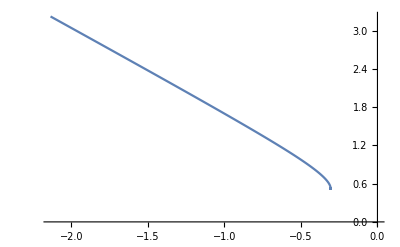

```mathematica
ListLinePlot[{Log10[#[[1]]],Log10[#[[2]]]} & /@ KerraOmegaList[2,0,{0,2},Im]]
```

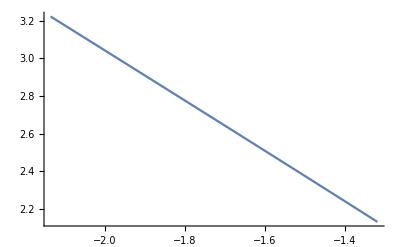

```mathematica
ListLinePlot[{Log10[#[[1]]],Log10[#[[2]]]} & /@ Take[KerraOmegaList[2,0,{0,2},Im],1000]]
```

```mathematica
LinearModelFit[{Log10[#[[1]]],Log10[#[[2]]]} & /@ Take[KerraOmegaList[2,0,{0,2},Im],200],la,la]
```

FittedModel[0.381638187030585079421879-1.33062851146495529587956 la]

```mathematica
10^(0.3795292215353835932402511199566235217207760948381210822319`24.915855359994442-1.3316858572518260764661625470375355633836895304600045974153`24.915855359994442 Log10[a])
```

2.39623397509646391899708/a^1.33168585725182607646616

```mathematica
fm=NonlinearModelFit[Take[KerraOmegaList[2,0,{0,2},Im],200],c1 a^(-c2),{{c1,2.39623},{c2,1.3317}},a]
```

FittedModel[2.41495126338570444628635/a^(«77»)]

```mathematica
fm2=NonlinearModelFit[Take[KerraOmegaList[2,0,{0,2},Im],200],c1 a^(-4/3),{{c1,2.39623}},a]
```

FittedModel[2.37760640199927464355373/a^(4/3)]

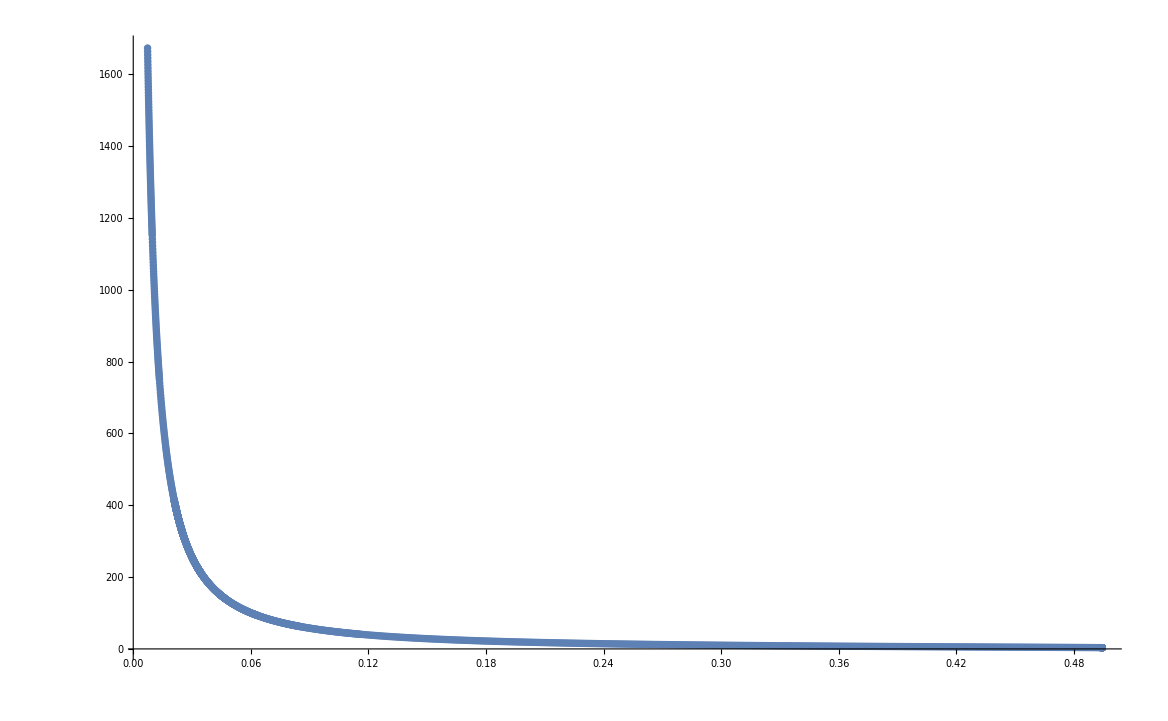

```mathematica
Show[ListPlot[KerraOmegaList[2,0,{0,2},Im]],Plot[fm2[a],{a,0.0001,0.4}],PlotRange->All]
```

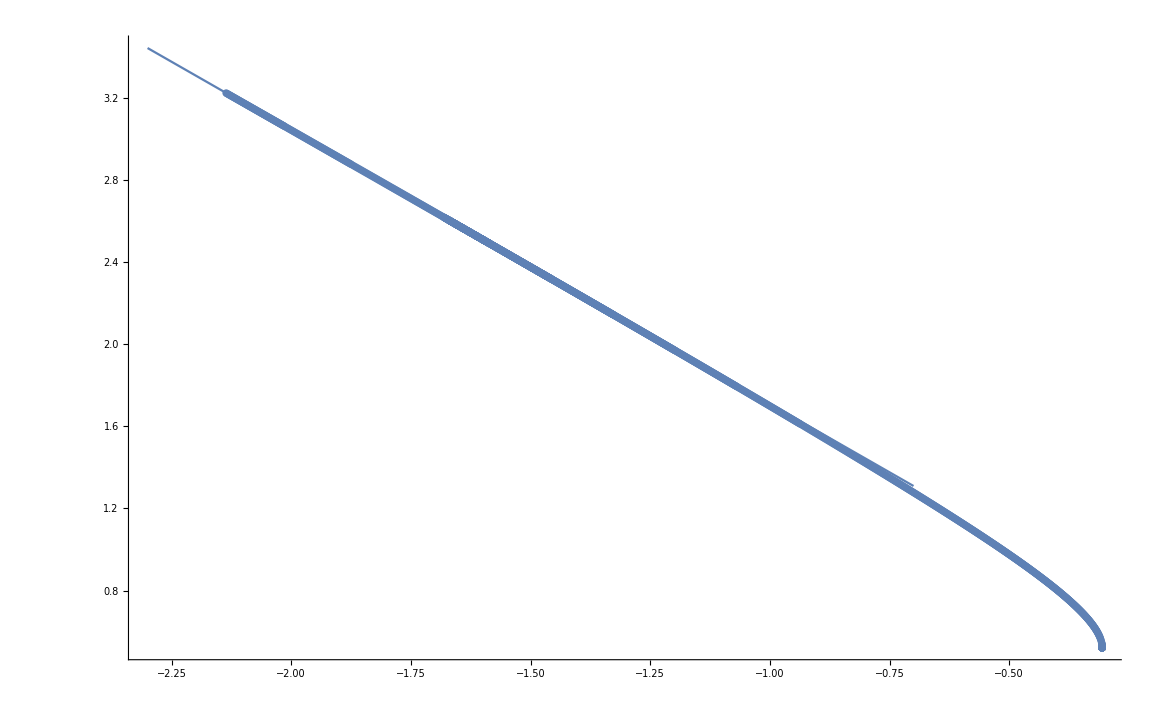

```mathematica
Show[ListPlot[{Log10[#[[1]]],Log10[#[[2]]]} & /@ KerraOmegaList[2,0,{0,2},Im]],Plot[Log10[fm2[10^la]],{la,-2.3,-0.7}],PlotRange->All]
```

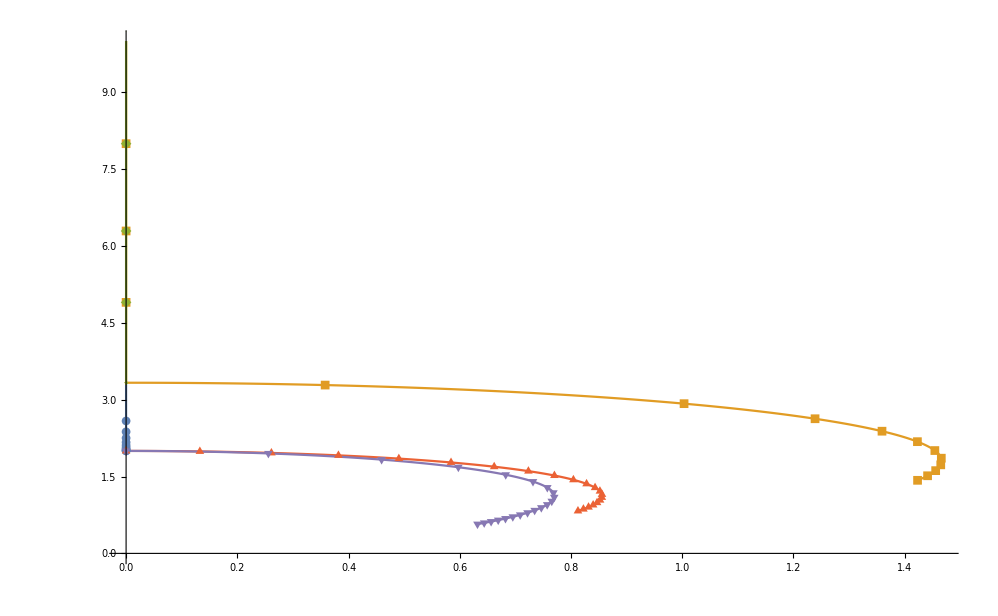

```mathematica
ModePlotOmega[2,0,OTmultiple->{{0,3}},PlotRange->{Automatic,{0,10}}]
```

```mathematica
ModePlotOmega[2,0,{0,2}]
```

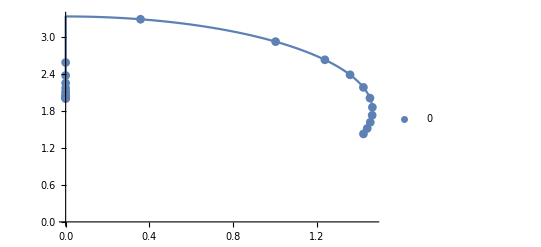

```mathematica
ModePlotOmega[2,0,PlotLegends->Automatic]
```

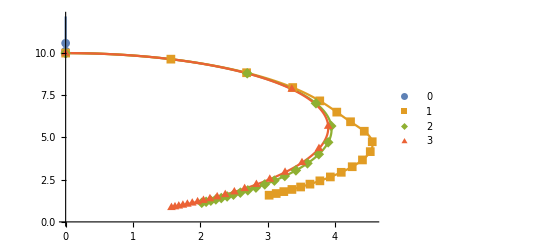

```mathematica
ModePlotOmega[3,0,PlotLegends->Automatic]
```

```mathematica
Head[Re]
```

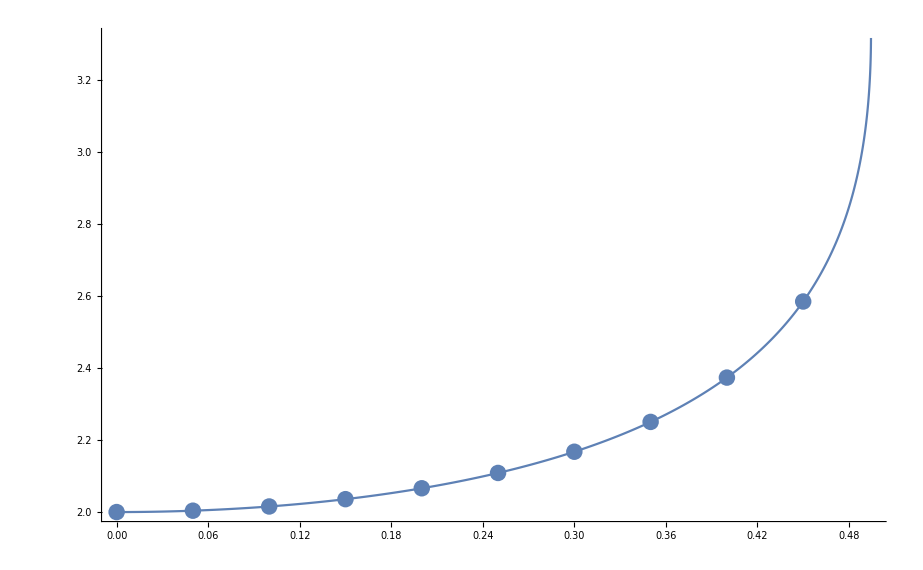

```mathematica
Show[ListLinePlot[KerraOmegaList[2,0,0,Im],PlotRange->All],ListPlot[KerraOmegaListS[2,0,0,Im],PlotRange->All]]
```

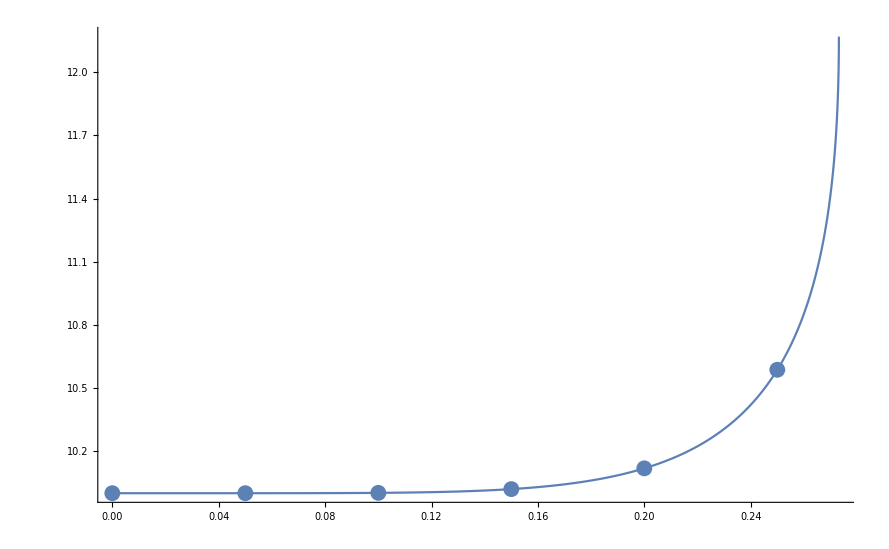

```mathematica
Show[ListLinePlot[KerraOmegaList[3,0,0,Im],PlotRange->All],ListPlot[KerraOmegaListS[3,0,0,Im],PlotRange->All]]
```

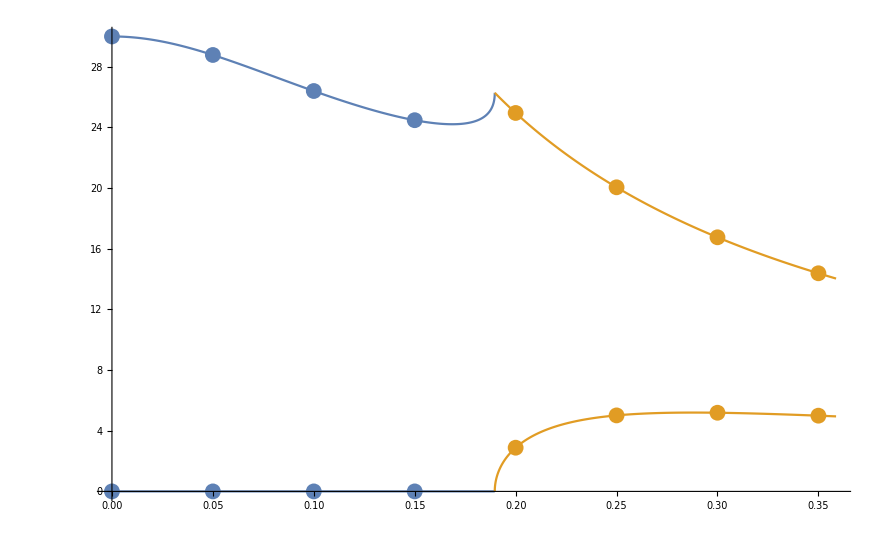

```mathematica
Show[ListLinePlot[{KerraOmegaList[4,0,{0,0},Re],KerraOmegaList[4,0,{0,1},Re]},PlotRange->All],ListLinePlot[{KerraOmegaList[4,0,{0,0},Im],KerraOmegaList[4,0,{0,1},Im]},PlotRange->All],ListPlot[{KerraOmegaListS[4,0,{0,0},Re],KerraOmegaListS[4,0,{0,1},Re]},PlotRange->All],ListPlot[{KerraOmegaListS[4,0,{0,0},Im],KerraOmegaListS[4,0,{0,1},Im]},PlotRange->All],PlotRange->All]
```

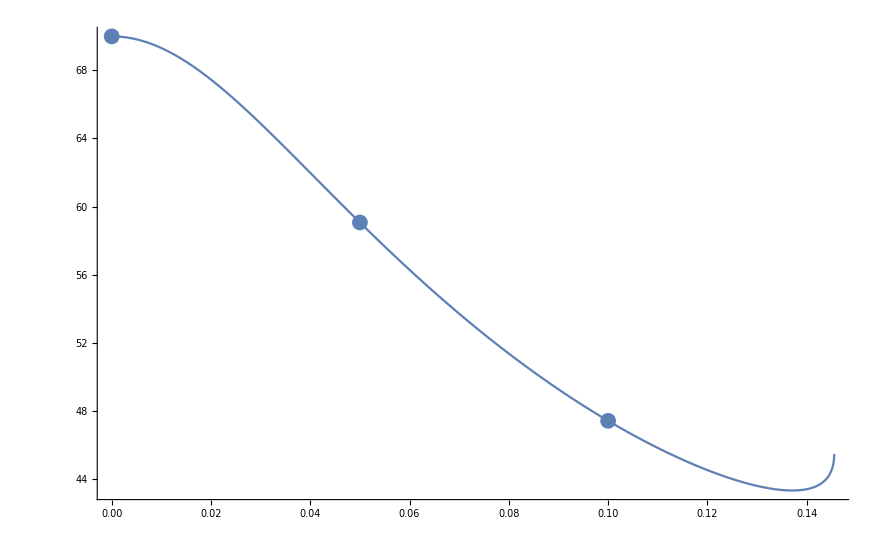

```mathematica
Show[ListLinePlot[KerraOmegaList[5,0,0,Im],PlotRange->All],ListPlot[KerraOmegaListS[5,0,0,Im],PlotRange->All]]
```

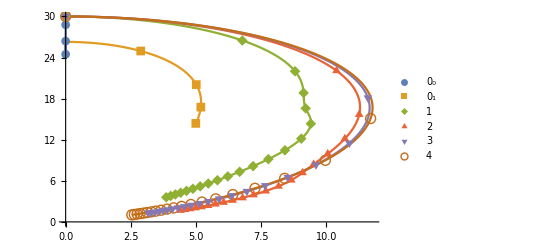

```mathematica
ModePlotOmega[4,0,OTmultiple->{{0,2}},PlotLegends->Automatic]
```

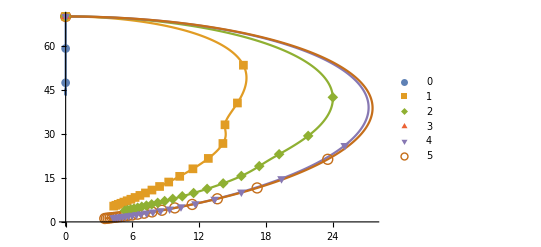

```mathematica
ModePlotOmega[5,0,PlotLegends->Automatic]
```

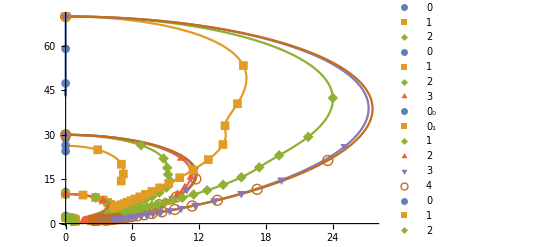

```mathematica
Show[ModePlotOmega[2,0,PlotLegends->Automatic],ModePlotOmega[3,0,PlotLegends->Automatic],ModePlotOmega[4,0,OTmultiple->{{0,2}},PlotLegends->Automatic],ModePlotOmega[5,0,PlotLegends->Automatic],PlotRange->All]
```

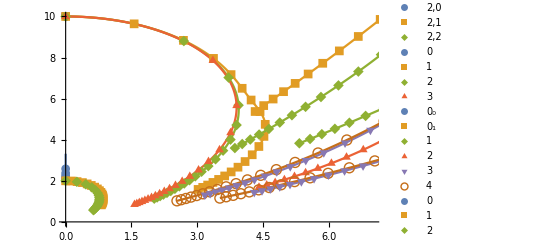

```mathematica
Show[ModePlotOmega[2,0,PlotLegends->{"2,0","2,1","2,2"}],ModePlotOmega[3,0,PlotLegends->Automatic],ModePlotOmega[4,0,OTmultiple->{{0,2}},PlotLegends->Automatic],ModePlotOmega[5,0,PlotLegends->Automatic],PlotRange->{{0,7},{0,10}}]
```

```mathematica
N[KerrTTML[5,0,0][[-1,1]]]
```

0.145536

```mathematica
SchwarzschildTTML[2,0]
```

Computing (l=2,n=0)

{-2. ⅈ,0,300,-14,0}

```mathematica
KerrTTML[2,2,0]
```

{{0,{-2. ⅈ,0,300,-8,0,300,0,331776.000000000000000207,24},{4,4,{1,0,0,0}}},{1/2000,{0.0026666551652701076511193-1.99999487833507862105213 ⅈ,0,300,-8,0,300,0,331776.51960208453111348,24},{3.99999717990467919850917+0.00266666174017775079459347 ⅈ,5,{0.999999982363372167617326,2.45198052526124432820479×10^-7-0.000187811592969986840825002 ⅈ,-2.78872753541199755742722×10^-8-7.48167775047200787673528×10^-11 ⅈ,-1.29606779995223449195122×10^-14+3.21043318440435795820121×10^-12 ⅈ,3.04926317239405376162335×10^-16+1.64480446339400126503193×10^-18 ⅈ}}},{3/2000,{0.00799968947809541011313172-1.99995390704600226284234 ⅈ,0,300,-8,0,300,0,331780.676075117104566321,24},{3.99997461989802179727934+0.00799986699017724450226571 ⅈ,5,{0.999999841274415211014372,2.20670893774846144035319×10^-6-0.000563423652173946337065283 ⅈ,-2.50971528877109553218675×10^-7-2.01994211610712568678682×10^-9 ⅈ,-1.04973026766727508503315×10^-12+8.66725489042023327544275×10^-11 ⅈ,2.46948254168269799281964×10^-14+3.99642989655920669598578×10^-16 ⅈ}}}}

```mathematica
SchwarzschildTTML[3,0]
```

Computing (l=3,n=0)

{-10. ⅈ,0,300,-14,0}

```mathematica
KerrTTMLSequence[2,2,0,-8,SeqDirection->Forward]
```

Set $MinPrecision = 24

KerrTTML[2,2,0] sequence exists with 2 entries

Untested section of code! 2

ModeSol a=0.0015 ω=0.00799969-1.99995 ⅈ Alm=3.99997+0.00799987 ⅈ

KerrModes`Private`AdaptCheck3::incorrectam: Incorrect Δa(-)

$Aborted

```mathematica
KerrTTMLSequence[2,2,0,-8,SeqDirection->Forward,ModeGuess->{0.005348-2*I,4}]
```

Set $MinPrecision = 24

KerrTTML[2,2,0] sequence exists with 3 entries

Untested section of code! 1

Guesses set: 0.005348-2. ⅈ : 4 : 300 : 5

Part::partd: Part specification {«1»}⟦0,1⟧ is longer than depth of object.

Part::partd: Part specification {«1»}⟦0,2,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

KerrModes`Private`KerrModeSequence::invalidcall: Invalid call to ModeSolution

$Aborted

```mathematica
Clear[KerrTTML]
```

```mathematica
N[KerrTTML[2,0,{0,0}][[-1,1]]]
```

0.493375

```mathematica
KerrModeMakeMultiplet[2,0,0]
```

```mathematica
Show[ModePlotOmega[2,0,{0,0}],ModePlotOmega[2,0,{0,1}],PlotRange->All]
```

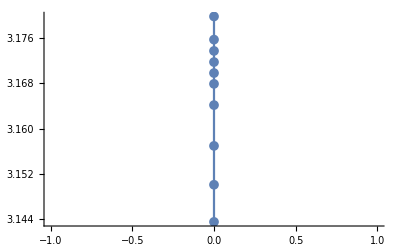

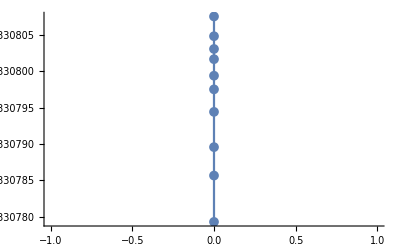

```mathematica
ListLinePlot[Chop[Take[KerrOmegaList[2,0,{0,0}],-10]],PlotRange->Automatic,PlotMarkers->{Automatic, 10}]
```

```mathematica
ShortenModeSequence[2,0,{0,1},1]
```

Original Length of KerrQNM[2,0,{0,1}]=117

Removing first 1 elements

```mathematica
<<"~/Research/KerrQNM/KerrModes/TTMLmodes.dat";
```

```mathematica
<<"~/Research/KerrQNM/KerrModes/QNMmodes.dat";
```

```mathematica
2.0299287138129135*^-39-3.1841050359735195 ⅈ
```

```mathematica
5.20388156758105+2.0875615531508266*^-39 ⅈ
```

```mathematica
Options[KerrTTMLSequence]
```

{CurvatureRatio→1/2,ExtrapolationOrder→2,JacobianStep→-10,Maxblevel→20,Maximalaϵ→10,MaxΔω→0.01,Minblevel→0,ModeaStart→0,ModeGuess→0,ModePrecision→24,NoNegω→False,RadialCFDepth→1,RadialCFDigits→8,RadialCFMinDepth→300,RadialDebug→0,RadialRelax→1,Rootϵ→Null[],SeqDirection→Forward,SolutionDebug→0,SolutionIter→50,SolutionOscillate→10,SolutionRelax→1,SolutionSlow→10,SolutionWindowl→1/2,SolutionWindowt→1/3,SpinWeight→-2}

```mathematica
KerrTTMLSequence[2,0,{0,0},-8,Minblevel->26,Maxblevel->30,SolutionDebug->0,RadialDebug->0]
```

Set $MinPrecision = 24

KerrTTML[2,0,{0,0}] sequence exists with 596 entries

ModeSol a=0.4944459549188613892 ω=0.0000101558-3.33081 ⅈ Alm=5.31276+7.32555×10^-6 ⅈ

ModeSol+ a=0.4944459548890590668 ω=4.79096×10^-24-3.33079 ⅈ Alm=5.31275+3.45578×10^-24 ⅈ

ModeSol+ a=0.494445954903960228 ω=-2.00732×10^-23-3.33079 ⅈ Alm=5.31275-1.44791×10^-23 ⅈ

ModeSol+ a=0.4944459549114108086 ω=1.43549×10^-21-3.3308 ⅈ Alm=5.31276+1.03544×10^-21 ⅈ

ModeSol+ a=0.4944459549151360989 ω=3.8389×10^-6-3.33081 ⅈ Alm=5.31276+2.76906×10^-6 ⅈ

ModeSol+ a=0.494445954916998744 ω=7.67716×10^-6-3.33081 ⅈ Alm=5.31276+5.53766×10^-6 ⅈ

ModeSol- a=0.4944459549132734537 ω=6.81813×10^-19-3.3308 ⅈ Alm=5.31276+4.91802×10^-19 ⅈ

ModeSol+ a=0.4944459549142047763 ω=4.96472×10^-21-3.33081 ⅈ Alm=5.31276+3.58113×10^-21 ⅈ

ModeSol- a=0.4944459549123421311 ω=-8.75194×10^-22-3.3308 ⅈ Alm=5.31276-6.31291×10^-22 ⅈ

ModeSol- a=0.4944459549076855183 ω=-1.29786×10^-21-3.3308 ⅈ Alm=5.31275-9.36163×10^-22 ⅈ

ModeSol-- a=0.4944459549095481634 ω=1.58218×10^-29-3.3308 ⅈ Alm=5.31275+1.14125×10^-29 ⅈ

ModeSol- a=0.4944459548965096474 ω=-3.50654×10^-22-3.33079 ⅈ Alm=5.31275-2.52932×10^-22 ⅈ

ModeSol- a=0.4944459548741579056 ω=-5.32138×10^-25-3.33078 ⅈ Alm=5.31274-3.83837×10^-25 ⅈ

ModeSol- a=0.494445954829454422 ω=2.64273×10^-23-3.33077 ⅈ Alm=5.31273+1.90623×10^-23 ⅈ

ModeSol+ a=0.4944459548443555832 ω=1.92852×10^-23-3.33077 ⅈ Alm=5.31273+1.39106×10^-23 ⅈ

ModeSol- a=0.4944459548145532608 ω=3.80976×10^-24-3.33076 ⅈ Alm=5.31273+2.74802×10^-24 ⅈ

Decreasing Δa, blevel = 29

ModeSol a=0.4944459549207240343 ω=0.0000121385-3.33081 ⅈ Alm=5.31276+8.75566×10^-6 ⅈ

ModeSol a=0.4944459549225866795 ω=0.0000138399-3.33081 ⅈ Alm=5.31276+9.98297×10^-6 ⅈ

Increasing Δa, blevel = 28

ModeSol a=0.4944459549263119698 ω=0.0000167316-3.33081 ⅈ Alm=5.31276+0.0000120688 ⅈ

Increasing Δa, blevel = 27

ModeSol a=0.4944459549337625504 ω=0.0000213718-3.33081 ⅈ Alm=5.31276+0.0000154158 ⅈ

Increasing Δa, blevel = 26

ModeSol a=0.4944459549486637115 ω=0.0000284669-3.33081 ⅈ Alm=5.31276+0.0000205337 ⅈ

ModeSol a=0.4944459549635648727 ω=0.0000341171-3.33081 ⅈ Alm=5.31276+0.0000246092 ⅈ

$Aborted

```mathematica
N[KerrTTML[2,0,{0,0}][[{-2,-1},1]],20]
```

{0.49444595491327345371,0.49444595491420477629}

```mathematica
ShortenModeSequence[2,0,{0,0},-9]
```

Original Length of `1`[`2`,`3`,`4`] = `5`KerrModes`Private`SpinWeightTable20{0,0}618

Removing last -9 elements

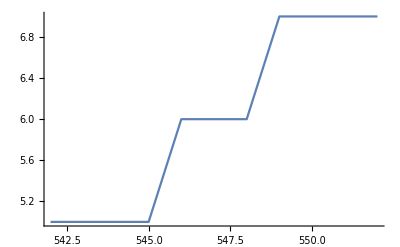

Set $MinPrecision = 24

```mathematica
KerrTTMLRefineSequence[2,0,{0,0},-8,RefinementAction->FixAdapt,Maxblevel->7,RefinementPlot->SeqLevel,Refinement->{-12,-1},Index->True]
```

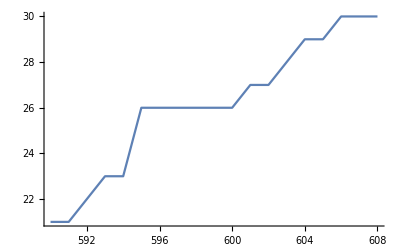

```mathematica
KerrTTMLRefineSequence[2,0,{0,0},-8,RefinementAction->None,Maxblevel->4,RefinementPlot->SeqLevel,Refinement->{-20,-1},Index->True]
```

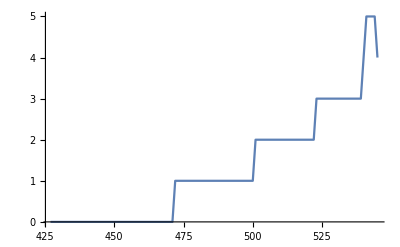

```mathematica
KerrTTMLRefineSequence[2,0,{0,0},-8,RefinementAction->RemoveLevels,Maxblevel->4,RefinementPlot->SeqLevel,Refinement->{-120,-1},Index->True]
```

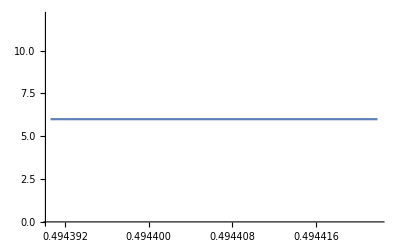

Set $MinPrecision = 24

debug : s = -2 l = 2 m = 0 ϵ = -8 relax = 1 index0 = 567 blevel = 6 forward = False incflag = False

ModeSol+ a=0.4944296875 ω=2.03323×10^-28-3.3113 ⅈ Alm=5.29863+1.46115×10^-28 ⅈ

ModeSol- a=0.4944140625 ω=3.68686×10^-31-3.30356 ⅈ Alm=5.29301+2.64549×10^-31 ⅈ

debug : s = -2 l = 2 m = 0 ϵ = -8 relax = 1 index0 = 566 blevel = 6 forward = False incflag = True

ModeSol- a=0.4943984375 ω=1.33542×10^-23-3.29762 ⅈ Alm=5.28867+9.57087×10^-24 ⅈ

```mathematica
KerrTTMLRefineSequence[2,0,{0,0},-8,RefinementAction->RefineAdapt,Minblevel->7,RefinementPlot->SeqLevel,Refinement->{-4,-1},SolutionDebug->0,RadialDebug->0]
```

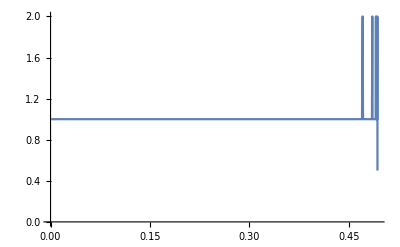

```mathematica
KerrTTMLRefineSequence[2,0,{0,0},-8,RefinementAction->None,RefinementPlot->StepRatio]
```

```mathematica
t=Null[]
```

Null[]

```mathematica
MemberQ[{QNM,TTML,TTMR},QNM]
```

True

```mathematica
QNM!=Null[]
```

QNM≠Null[]

Part::partd: Part specification KerrQNM[2,0,{8,0}]⟦1,2,1⟧ is longer than depth of object.

Part::partd: Part specification KerrQNM[2,0,{8,0}]⟦2,2,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

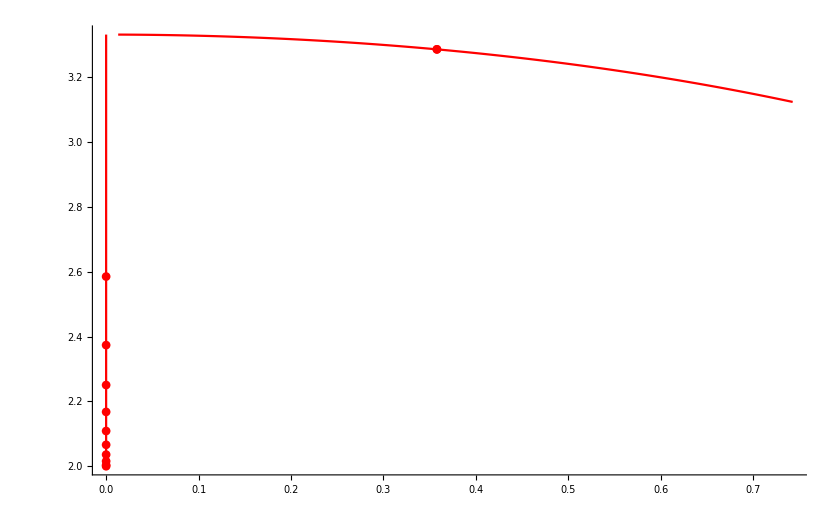

```mathematica
Show[ModePlotOmega[2,0,{0,0},PlotStyle->Red],ModePlotOmega[2,0,{0,1},PlotStyle->Red],ModePlotOmega[2,0,{8,0},ModeType->QNM],PlotRange->All]
```

```mathematica
?ShortenModeSequence
```

ShortenModeSequence[l,m,n,N] removes the first N elements of the Mode sequence (l,m,n)
if N>0, and removes the last N elements if N<0.

Options:
	 ShortenBy→Drop : Drop, Take
		 If 'Take' is chosen, the first N elemets are kept if N>0, and the last N elements
		 are kept if N<0.

```mathematica
KerrTTMLSequence[2,0,{0,1},-8,SeqDirection->Backward,ModeaStart->{51/100,0.578-3.21ⅈ,4}]
```

$Aborted

```mathematica
ShortenModeSequence[2,1,0,-5,ShortenBy->Take]
```

Original Length of KerrQNM[2,1,0]=30

Taking last -5 elements

```mathematica
N[KerrTTML[2,1,0][[1,1]]]
```

0.03

```mathematica
KerrTTML[2,0,{0,0}][[-1]]
```

{8101001/16384000,{-2.59221938844357377362308×10^-27-3.32932464333632508809299 ⅈ,0,300,-8,1.05427856406349503051469×10^-19,300,0,0.654387451804623391671247,24},{5.31169089006987495148787-1.86929049226304246652264×10^-27 ⅈ,12,{0.926314398664427651686731,-2.43605512448961034437431×10^-28-0.362297525389928649821131 ⅈ,-0.101203172569303999014166+1.44835657915437095439063×10^-28 ⅈ,4.52699248059806435096392×10^-29+0.020691886304687763601274 ⅈ,0.00341752527281805138651751-1.01091317404582626241193×10^-29 ⅈ,-1.74497194733624481485521×10^-30-0.000468058577520540482725929 ⅈ,-0.0000551013052586024172915862+2.48084298442211282297944×10^-31 ⅈ,2.98995697994554160239674×10^-32+5.66643235812711576651505×10^-6 ⅈ,5.18537495346009658744474×10^-7-3.13850162493409875158105×10^-33 ⅈ,-2.91415986051870476043666×10^-34-4.26754202753149016890482×10^-8 ⅈ,-3.19443226670194558835269×10^-9+2.42952301019190785071037×10^-35 ⅈ,1.83926163720485453009745×10^-36+2.19370530272997909914795×10^-10 ⅈ}}}

```mathematica
KerrModeMakeMultiplet[2,1,0]
```

```mathematica
KerrTTML[2,1,{0,0}]
```

```mathematica
?KerrModeMakeMultiplet
```

```mathematica
KerrTTMLSequence[2,1,0,-8,SeqDirection->Forward,ModeaStart->{1/100,0.026-2.0ⅈ,4.0}]
```

$Aborted

```mathematica
?ShortenModeSequence
```

```mathematica
KerrTTMLSequence[2,1,0,-8,SeqDirection->Forward,ModeaStart->{1/100,0.026-2.0ⅈ,4.0}]
```

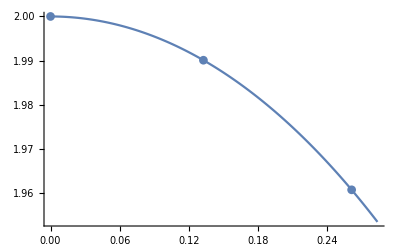

```mathematica
ModePlotOmega[2,0]
```

```mathematica
Options[ModeSolution]
```

{JacobianStep→-10,NoNegω→False,QNMPrecision→24,RadialCFDigits→8,RadialCFMinDepth→300,RadialDebug→0,RadialRelax→1,RCFPower→Null[],Rootϵ→Null[],SolutionDebug→0,SolutionIter→50,SolutionOscillate→10,SolutionSlow→10}

```mathematica
SelectMode[PolynomialMode]
```

Mode set to find Polynomial solutions

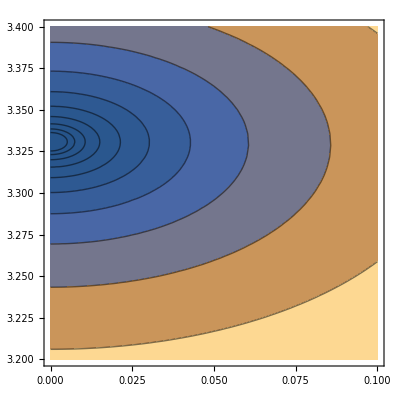

```mathematica
ContourPlot[Abs[PlotModeFunction[0,-2,0,8101001/16384000,4,ωr-ⅈ ωi,0,15]],{ωr,0,0.1},{ωi,3.2,3.4},Contours->{1/128,1/64,1/32,1/16,1/8,1/4,1/2,1,2,4,8}]
```

```mathematica
Plot3D[{Re[PlotModeFunctionL[0,-2,0,1579/3200,1,ωr-ⅈ ωi,0,15]],Im[PlotModeFunctionL[0,-2,0,1579/3200,1,ωr-ⅈ ωi,0,15]]},{ωr,-0.02,0.02},{ωi,3.15,3.23}]
```

-Graphics3D-

```mathematica
?PlotModeFunction
```

Arguments: n,s,m,a,Alm,ω,Nrcf,Nm
	 n -> Overtone level (integer).
	 s -> SpinWeight (integer).
	 m -> Azimuthal index (integer).
	 a -> Dimensionless spin parameter(rational or integer).
	 Alm -> Angular separation constant (integer).
	 Nrcf -> How deep into the continued fraction (integer).
	 Nm -> Number of azimuthal indecies(integer).

When in ContinuedFractionMode, package will require input for all the arguments and will use SelectMode
	 to replace ModeFunction with RadialCFRem.
When in PolynomialMode, n and Nrcf are not used in this plot function. Put dummy value in place.
PolynomialMode will use SelectMode to replace Modefunction with Starobinsky.

```mathematica
?ModeSolution
```

QNMSolution[n,s,l,m,a,ωg,Almg,ϵ,relax,Nrcf,Nm,ω0,Alm0,rl,rt] finds a solution of the coupled radial and angular Teukolsky equations with spin-weight s, 'magnetic' index m, and dimensionless angular momentum a.  ωg and Almg are initial guesses for the frequency and separation constant, which are assumed to be associated with azimuthal index l and overtone index n.

	The solution is found by iteration, calling AngularSpectralRoot and RadialLentzRoot until the magnitude of the change produced by either is less than 10^ϵ.  'relax' is an initial under-relaxation parameter used in updating the current guesses. For the radial equation, the continued fraction is truncated at the Nrcf^th term.  For the angular equation, Nm sets the size of the spectral approximation matrix.

	ω0, Alm0, rl, and rt are used to specify solution windows centered around the initial guesses ωg and Almg.  ω0 and Alm0 represent the prior solutions in a sequence of solutions.  |ω0-ωg| and |Alm0-Almg| set a length scale d for each solution.  The window for each solution is a portion of an anulus centered on the prior solution.  The difference between the inner and outer rings of the anulus is 2*rl*d with the guess solution centered between.  The width of the wedge is 2*rt*d along the outer ring.  Solutions falling outside the solution window for either quantity are rejected.  If rl=0 or rt=0, the solution is always accepted.

Options:
	 SolutionDebug→0 : Integer
		 Verbosity of debugging output for solutions iteration.  Increasing
		 value increases verbosity.
	 RadialDebug→0 : Integer
		 Verbosity of debugging output.  Increasing value increases verbosity.
	 RadialRelax→1: Rational(or Integer)
		 Under-relaxation parameter.
	 JacobianStep→-10
		 Log10 of relative step size used in numerical evaluation of the 
		 Jacobian in Newton's method.

```mathematica
?PlotModeFunction
```

Arguments: n,s,m,a,Alm,ω,Nrcf,Nm
	 n -> Overtone level (integer).
	 s -> SpinWeight (integer).
	 m -> Azimuthal index (integer).
	 a -> Dimensionless spin parameter(rational or integer).
	 Alm -> Angular separation constant (integer).
	 Nrcf -> How deep into the continued fraction (integer).
	 Nm -> Number of azimuthal indecies(integer).

When in ContinuedFractionMode, package will require input for all the arguments and will use SelectMode
	 to replace ModeFunction with RadialCFRem.
When in PolynomialMode, n and Nrcf are not used in this plot function. Put dummy value in place.
PolynomialMode will use SelectMode to replace Modefunction with Starobinsky.

```mathematica
SchwarzschildTTML[2,0,RadialDebug->4,SchDebug->1]
```

Computing (l=2,n=0)

RadialLentzStep :{KerrModes`Private`δωr→-9.99500374737656280568554×10^-6,KerrModes`Private`δωi→0.000999750149899958625930798} : {-0.576143985599936531025921-0.00576288000000000015423491 ⅈ,0}

δω=-9.99500374737656280568554×10^-6+0.000999750149899958625930798 ⅈ  root=0.576172806481592181039581

ω=4.99625262343801234499851×10^-9-2.00000024985009993123995 ⅈ

RadialLentzStep :{KerrModes`Private`δωr→-4.9962519992810206336147×10^-9,KerrModes`Private`δωi→2.49850084331214418590972×10^-7} : {-0.000143913666546010033345319-2.87784187061478967805879×10^-6 ⅈ,0}

δω=-4.9962519992810206336147×10^-9+2.49850084331214418590972×10^-7 ⅈ  root=0.000143942437774787012507994

Conv.Rate: 4000.80021491544868023167 : False

ω=6.24156991711383808045256×10^-16-2.00000000000001560002553 ⅈ

Set $MinPrecision =28

RadialLentzStep :{KerrModes`Private`δωr→-6.241569917113789396127541818×10^-16,KerrModes`Private`δωi→1.560002552656791373291584416×10^-14} : {-8.98561470330318828587217626×10^-12-3.595144272257598776511884402×10^-13 ⅈ,0}

δω=-6.241569917113789396127541818×10^-16+1.560002552656791373291584416×10^-14 ⅈ  root=8.992803913107519250534493049×10^-12

Conv.Rate: 1.600640036006678063732783896×10^7 : False

ω=4.868432501885096229986790674×10^-30-2. ⅈ

Set $MinPrecision =44

RadialLentzStep :{KerrModes`Private`δωr→-4.8684325018850962299867906736828033984999319×10^-30,KerrModes`Private`δωi→6.0742806119807339645384126163805259310871118×10^-29} : {-3.4987856325009027635741256671407633578783776×10^-26-2.8042171210858154284723914282116307745013191×10^-27 ⅈ,0}

δω=-4.8684325018850962299867906736828033984999319×10^-30+6.0742806119807339645384126163805259310871118×10^-29 ⅈ  root=3.5100053046707280435110922889030976789890763×10^-26

Conv.Rate: 2.5620485248671325973827021812564446137491955×10^14 : False

SetPrecision::precsm: Requested precision 24 is smaller than $MinPrecision. Using $MinPrecision instead.

KerrModes`Private`RadialLentzStep::increase: Excessive increase in Precision, Abort

$Aborted

```mathematica
$MinPrecision=24
```

24

```mathematica
SelectMode[PolynomialMode]
```

Mode set to find Polynomial solutions

```mathematica
Plot3D[Abs[PlotModeFunctionL[0,-2,1,50/100,1,ωr-ⅈ ωi,300,15]],{ωr,0,1},{ωi,1,2}]
```

-Graphics3D-

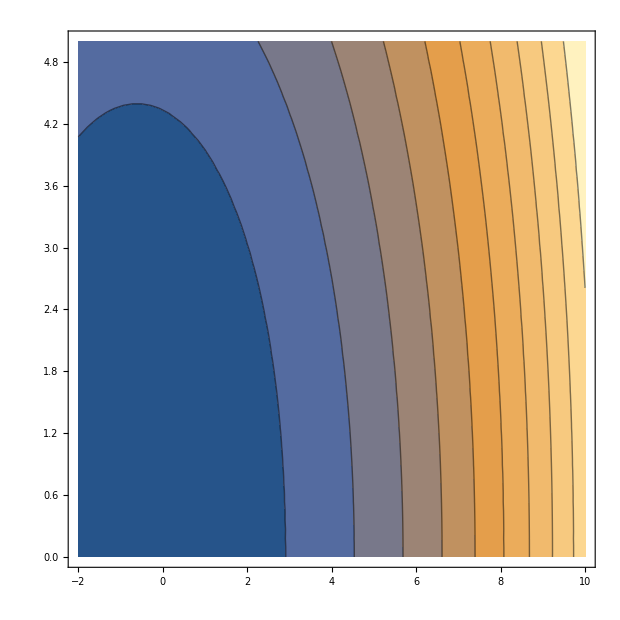

```mathematica
ContourPlot[Abs[PlotModeFunctionL[0,-2,-2,1/8,1,ωr-ⅈ ωi,3000,15]],{ωr,-2,10},{ωi,0,5},Contours->10]
```

```mathematica
Plot3D[{Re[PlotModeFunctionL[0,-2,-1,1/2,1,ωr-ⅈ ωi,3000,15]],Im[PlotModeFunctionL[0,-2,-1,1/2,1,ωr-ⅈ ωi,3000,15]]},{ωr,0,5},{ωi,0,5}]
```

-Graphics3D-

```mathematica
Plot3D[{Re[RadialCFRem[0,-2,0,0,4,ωr-ⅈ ωi,300][[1]]],Im[RadialCFRem[0,-2,0,0,4,ωr-ⅈ ωi,300][[1]]]},{ωr,0,4},{ωi,0,4}]
```

-Graphics3D-

```mathematica
RadialCFRem[0,-2,0,0,10,-ⅈ 10,2]
```

RadialCFRem[0,-2,0,0,10,-10 ⅈ,2]

```mathematica
SchwarzschildTTML[2,0,RadialDebug->1,SchDebug->0]
```

Computing (l=2,n=0)

Have made it into RadialCFRem

Have made it into RadialCFRem

Have made it into RadialCFRem

«17 more identical outputs»

KerrModes`Private`RadialLentzStep::increase: Excessive increase in Precision, Abort

$Aborted

```mathematica
?SchwarzschildTTML
```

SchwarzschildTTML[l,n] computes the Quasi-Normal Mode solutions for overtone n of mode l.  The mode is computed to an accuracy of 10^-14.  For given 'l', if solutions with overtones (n-1) and (n-2) have not been computed, then the routine is recersively called for overtone '(n-1).  If no solutions exist for mode l, then the first two overtones of (l-1) and (l-2) are used to extrapolate initial guesses for these modes.

Options:
	 SpinWeight→Null : -2,-1,0
		 The spin weight must be set via a call to SetSpinWeight before any KerrTTML
		 function call.
	 ModePrecision→24
	 JacobianStep→-10
		 The radial solver make use of numerical derivatives.  The relative step size
		 is set to 10^JacobianStep.
	 RadialCFMinDepth→300
		 The minimum value for the Radial Continued Fraction Depth.
	 RadialCFDepth→1
		 The initial Radial Continued Fraction Depth is usually taken from the prior 
		 solution in the sequence.  Fractional values reduce this initial value by that
		 fraction.  Integer values larger than RadialCFMinDepth are used as the new
		  initial value.
	 RadialRelax→1
		 Initial under-relaxation parameter used in Radial Newton iterations.
	 Rootϵ→-14
		 10^Rootϵ is the maximum allowed magnitude for the Radial Continued Fraction.
	 SchDebug→0 : 0,1,2,3,...
		 'Verbosity' level during the Schwarzschile iterations.
	 RadialDebug→0 : 0,1,2,3,...
		 'Verbosity' level during the Radial Newton iterations.